# LA 101 Gerald Farin 2011

## Reference: G. Farin and D. Hansford. Practical Linear Algebra. AK Peters, 2004.

## About this notebook

We present the critical concepts from the reference above. No knowledge of Linear Algebra is assumed; but some familiarity with Mathematica will be necessary. Each section starts with a text introduction, followed by Mathematica examples. These begin with input data and then use those to illustrate the concepts of the section. The idea is to play with the inputs and observe what happens. Number to be "played" with are in cyan. After having changed data, hit Shift+Enter to see the results.

We cover topics from the intuitive 2D and 3D cases.

This notebook is best read (and taught) in presentation mode. 

Here is a list of key terms, searchable with CTRL+F:
angle, area, determinant, dimension, dot product, eigenvalues, eigenvectors, ellipsoid, identity, inverse, linearly dependent, linear map, linear operations, length, line, linear space, linear system, matrix, normalized vector, null space, orthogonal, parametric equation, perpendicular, plane, point, powers of a matrix, product matrix, rank, rotation, scaling, singular matrix, spanned, sphere, subspace, symmetric matrix, transpose, unit vector, zero vector

## Linear Spaces

A linear space S is a a set whose elements may be combined to yield other elements in S. These basic operations are the linear operations.
For two elements  a and b in S, a linear combination is given by sa + tb, with s and t being real numbers (including neagtive numbers and 0). 

An example of a linear space is given by all 2D vectors v= (x
y) (typeset in boldface). Linear combinations are defined by 

	v = sa + tb = s(v
w) + t(x
y) = (sv + tx
sw+ty);  s,t ϵ ℝ.

A special vector is 0=(0
0), the zero vector.
	
In the following cell, the input vectors a and b are in black, and the result of the linear combinations are red. Note that as we change s, the result changes parallel to a, and as we change t, it changes parallel to b.

```mathematica
a = {4,1};   (*in blue *)
b= {0,1};  (* in green *)

arrowa={Arrowheads[Large],Arrow[{{0,0},a}]};
arrowb ={Arrowheads[Large],Arrow[{{0,0},b}]};

Manipulate[
Graphics[{Blue,arrowa, Green,arrowb,Red,{Arrowheads[Large],Arrow[{{0,0},s*a+t*b}]} },PlotRange->{{-1,2},{-1,2}}],{{s,0.5},-1,1},{{t,0.5},-1,1}, Alignment->Left]
```

## Linear Dependence and Determinants

Two vectors a and b are called linearly dependent if one can be expressed in terms of the other:

	b=ra.
	
Else, they are linearly independent.

The determinant of two vectors measures the area of the parallelogram spanned by them. If it is zero, then the vectors are linearly dependent. The area may also be negative. In the following cell, the determinant is displayed in a box on top of the graphic.

```mathematica
a1 = {1,0}; (* in black *)

arrowa1={Thick,Arrowheads[Large],Arrow[{{0,0},a1}]};

arrowplot=Graphics[arrowa];
Manipulate[
b1={s,t};  (*in red *)
arrowb1={Thick,Arrowheads[Large],Arrow[{{0,0},b1}]};

Graphics[{Green,Polygon[{{0,0},{1,0}, {1,0}+b1,b1}],Black,arrowa1,Red,arrowb1},PlotLabel->Style[Framed[Det[{{1,0},b1}]],20],Axes->True,PlotRange->{{-2,2},{-1,1}}],{{s,0.5},-1,1},{{t,0.5},-1,1}]
```

## Dot Product

Two vectors a=(v
w) and b=(x
y) define a dot product:

	ab=a.b=vx + wy.

If a.b=0, then a and b are perpendicular (also:orthogonal), i.e., they form a right angle.

In the following cell, b is changed in the Manipulate command (red), and a is given as fixed input (black). The dot product is displayed in a box.

```mathematica
a2 = {2,1}; (* in black *)

arrowa2={Thick,Arrowheads[Large],Arrow[{{0,0},a2}]};

arrowplot2=Graphics[arrowa2];
Manipulate[
b2={s,t};  (*in red *)
arrowb2={Thick,Arrowheads[Large],Arrow[{{0,0},b2}]};

Graphics[{arrowa2,Red,arrowb2},PlotLabel->Style[Framed[a2.b2],20],Axes->True,PlotRange->{{-2,2},{-1,1}}],{{s,0.5},-1,2},{{t,0.5},-1,1}]
```

The length of a vector a=(x
y) is given by

	||a||=√(a.a)=√(x^2+ y^2)

If a vector has length 1, it is called a unit vector or a normalized vector.

```mathematica
a3 = {1,3}//N;
lengtha3 = Sqrt[a3.a3]
```

3.16228

The angle (or rather, the cosine of it) between two vectors a and b is given by

	cos(a,b) = (a.b)/(||a||  ||b||).

## Points, Lines, and Vectors

A vector denotes a direction; it is not fixed anywhere in a coordinate system. A point defines a fixed position.
A line through a point p with direction v is given by the parametric equation
	
	l(t)=p + tv.

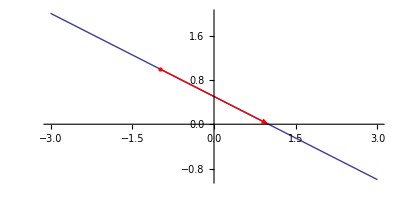

```mathematica
p={-1,1};
v={2,-1};
arrowpv={Red,Thick,Arrowheads[Large],Arrow[{p,p+v}]};
l[t_]:= p + t*v;


lineplot=ParametricPlot[l[t],{t,-1,2},PlotStyle-> Thick];
arrowplot=Graphics[arrowpv];
pplot=Graphics[{PointSize[Large],Red,Point[p]}];

Show[lineplot,arrowplot,pplot]
```

## Matrices

Linear combinations are also written in matrix form:

	c = sa + tb = s(v
w) + t(x
y) = (sv + tx
sw+ty)
		=(v | x
w | y)(s
t)
		
where (v | x
w | y) is a matrix M, and (s
t) is a vector v, abbreviated:

		c = Mv.
		
The action of M is called a linear map. Notationally,  we do not distiguish between a matrix and the corresponding linear map. 

If x=w=0, M is a scaling matrix.

 If 

	M=(cos α | -sin α
sin α | cos α),
	
M defines a rotation by α.

In the following cell, an input vector a is in green, its image b under the matrix mat is in red. The vector a traces out a circle, and b traces out an ellipse.

```mathematica
mat4= {{3,1},{1,2}};
(* be sure to try other matrices, for example mat4= {{-3,1},{1,2}};*)

Manipulate[a4={Cos[s],Sin[s]};(* in green, tracing out a circle *)
b4=mat4.a4;  (*in red *)

arrowa4={Thick,Arrowheads[Large],Arrow[{{0,0},a4}]};
arrowb4={Thick,Arrowheads[Large],Arrow[{{0,0},b4}]};

Graphics[{Green,arrowa4,Circle[],Red,arrowb4},Axes->True,PlotRange->{{-3,3},{-2,2}}],{{s,0},0,2Pi}]
```

All matrices map circles to ellipses.In the following cell, the original data are green, the mapped data (images) are red. Original points and corresponding image points are connected by straight lines. This is a static version of the previous cell.

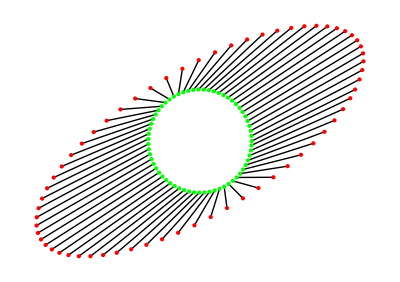

```mathematica
circpoints = Table[{Cos[t],Sin[t]},{t,0,2 Pi,0.1}];
ellpoints= Table[mat4.{Cos[t],Sin[t]},{t,0,2Pi,0.1}];
pplot=Graphics[{PointSize[Large],Green,Point[circpoints],Red, Point[ellpoints]}];

line[t_]:=Graphics[Line[ {mat4.{Cos[t],Sin[t]},{Cos[t],Sin[t]}}]];
lineplot=Table[line[t],{t,0,2Pi,0.1}];
Show[{lineplot,pplot}]
```

## Linearity

A linear map (defined by a matrix M) preserves linear combinations in the following sense. Assume three vectors a, b, c are related by a linear relationship

	       c = sa + tb.
	
If we now map a,b,c to Ma, Mb, Mc by a linear map M,  the original relationship will stay the same:

## Mc = sMa + tMb. In the following cell, we used a simplified version c = (1-s)a + sb. The vectors c and Mc are in red and blue, resp.; a,b are in yellow, and Ma, Mb are in cyan.

```mathematica
a = {-1,1}; (* yellow *)
b= {0,1}; (* yellow *)
mat = {{-3,1},{1,2}};
mata = mat.a;  (* cyan *)
matb = mat.b; (* cyan *)

arrowa={Arrowheads[Large],Arrow[{{0,0},a}]};
arrowb ={Arrowheads[Large],Arrow[{{0,0},b}]};
arrowmata={Arrowheads[Large],Arrow[{{0,0},mata}]};
arrowmatb ={Arrowheads[Large],Arrow[{{0,0},matb}]};

Manipulate[
Graphics[{Yellow,arrowa, arrowb,Cyan, arrowmata, arrowmatb,Red, {Arrowheads[Large],Arrow[{{0,0},(1-s)*a+s*b}]},Blue,{Arrowheads[Large],Arrow[{{0,0},(1-s)*mata+s*matb}]} },PlotRange->{{-1,4},{-1,3}}],{{s,0.5},0,1}]
```

## Matrix Operations

A vector v may be transformed using a linear map M,and then the result may again be transformed by using a linear map N:

N(Mv) = NMv.
N=(n_(1,1) | n_(1,2)
n_(2,1) | n_(2,2)),  M=(m_(1,1) | m_(1,2)
m_(2,1) | m_(2,2)).

The product matrix L=NM of the combined action has elements 
l_(i,j) where l_(i,j) is the dot product of the ith  row of N a nd the jth column of M.

Example:

 l_(2,1)=n_(2,1)m_(1,1) + n_(2,2)m_(2,1).	

Matrix products do not commute, i.e., MN ≠ NM (in general):

```mathematica
mat1={{1,1},{1,3}};
mat2={{0,2},{3,4}};
Print[MatrixForm[mat1.mat2]," ≠  ",MatrixForm[mat2.mat1]]
```

(3 | 6
9 | 14) ≠  (2 | 6
7 | 15)

We can define powers of a matrix:

M^2 = M.M, M^3= M.M^2  etc.

Some examples below. (Play with the matrix elements!)

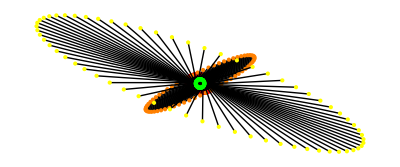

```mathematica
mat1= {{-3,3},{1.5,-2.5}};
trans=0;

(* action in red *)
circpoints = Table[{Cos[t],Sin[t]},{t,0,2 Pi,0.1}];
ellpoints= Table[mat.{Cos[t],Sin[t]},{t,0,2Pi,0.1}];
pplot=Graphics[{PointSize[Large],Green,Point[circpoints],Red, Point[ellpoints]}];
line[t_]:=Graphics[Line[ {mat.{Cos[t],Sin[t]},{Cos[t],Sin[t]}}]];
lineplot=Table[line[t],{t,0,2Pi,0.1}];


mat2= mat1^2; (*action on orange *)
circpoints2 = Table[{Cos[t],Sin[t]}+{trans,0},{t,0,2 Pi,0.1}];
ellpoints2= Table[mat2.{Cos[t],Sin[t]}+{trans,0},{t,0,2Pi,0.1}];
pplot2=Graphics[{PointSize[Large],Green,Point[circpoints2],Orange, Point[ellpoints2]}];
line2[t_]:=Graphics[Line[ {mat2.{Cos[t],Sin[t]}+{trans,0},{Cos[t],Sin[t]}+{trans,0}}]];
lineplot2=Table[line2[t],{t,0,2Pi,0.1}];


mat3= mat1^3; (*action in yellow *)
circpoints3 = Table[{Cos[t],Sin[t]}+{2trans,0},{t,0,2 Pi,0.1}];
ellpoints3= Table[mat3.{Cos[t],Sin[t]}+{2trans,0},{t,0,2Pi,0.1}];
pplot3=Graphics[{PointSize[Large],Green,Point[circpoints3],Yellow, Point[ellpoints3]}];
line3[t_]:=Graphics[Line[ {mat3.{Cos[t],Sin[t]}+{2trans,0},{Cos[t],Sin[t]}+{2trans,0}}]];
lineplot3=Table[line3[t],{t,0,2Pi,0.1}];

Show[{lineplot,pplot,lineplot2,pplot2,lineplot3,pplot3}]
```

Similarly,

	 M^0 = I  = (1 | 0
0 | 1) , the identity.

The matrix  M^-1 is the inverse of M:

M^-1 M=I. 

The inverse  M^-1 may be thought of as "undoing" the action of M.
	
Some matrices do not have an inverse: they are called singular. Their column vectors are linearly dependent.

```mathematica
mat={{1,1},{2,2}};

Print[MatrixForm[mat],",  ",MatrixForm[Inverse[mat]]]
```

Inverse::sing: Matrix {{1, 1}, {2, 2}} is singular.

(1 | 1
2 | 2),  Inverse[{{1,1},{2,2}}]

The transpose M^T of a matrix is obtained by "flipping" its off-diagonal elements:

```mathematica
mat={{-1,3},{4,-4}};

Print["matrix: ",MatrixForm[mat]," Transpose: ",MatrixForm[Transpose[mat]]]
```

matrix: (-1 | 3
4 | -4) Transpose: (-1 | 4
3 | -4)

The next cell shows the relationship between the actions of a matrix and its transpose.

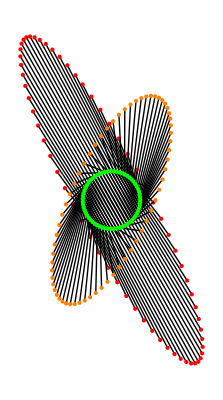

```mathematica
mat1= {{2,3},{-0.5,2}};
trans=0;

(* action in red *)
circpoints = Table[{Cos[t],Sin[t]},{t,0,2 Pi,0.1}];
ellpoints= Table[mat.{Cos[t],Sin[t]},{t,0,2Pi,0.1}];
pplot=Graphics[{PointSize[Large],Green,Point[circpoints],Red, Point[ellpoints]}];
line[t_]:=Graphics[Line[ {mat.{Cos[t],Sin[t]},{Cos[t],Sin[t]}}]];
lineplot=Table[line[t],{t,0,2Pi,0.1}];


mat2= Transpose[mat1];  (*action in orange*)
circpoints2 = Table[{Cos[t],Sin[t]}+{trans,0},{t,0,2 Pi,0.1}];
ellpoints2= Table[mat2.{Cos[t],Sin[t]}+{trans,0},{t,0,2Pi,0.1}];
pplot2=Graphics[{PointSize[Large],Green,Point[circpoints2],Orange, Point[ellpoints2]}];
line2[t_]:=Graphics[Line[ {mat2.{Cos[t],Sin[t]}+{trans,0},{Cos[t],Sin[t]}+{trans,0}}]];
lineplot2=Table[line2[t],{t,0,2Pi,0.1}];


Show[{lineplot,pplot,lineplot2,pplot2}]
```

A symmetric matrix is written as

	M=(m_(1,1) | a
a | m_(2,2)).
Thus

	M^T=M

for symmetric matrices.

Linear Systems

Given three vectors a,b,c, how can we write c as a linear combination of a and b, i.e., what are s and t in

	 sa + tb = c?
In matrix form, with M=[a,b] and v=(s
t):
	Mv = c.
	
Another way of saying this would be: what vector v is mapped to c by matrix M?
	
Solution: multiply both sides by the inverse M^-1 (assuming it exists!)

	v=M^-1c

```mathematica
a = {1,1};
b= {0,1};
c={1,1};

mat= {a,b};

v = Inverse[mat].c;
Print["direct solution: ", MatrixForm[v]];
Print["check: ",MatrixForm[mat],".",MatrixForm[v]," = ",MatrixForm[mat.v]];

(* Alternatively (and recommend for larger systems) *)

v=LinearSolve[mat,c];
Print["solution with LinearSolve: ", MatrixForm[v]];
Print["check: ",MatrixForm[mat],".",MatrixForm[v]," = ",MatrixForm[mat.v]];
```

direct solution: (0
1)

check: (1 | 1
0 | 1).(0
1) = (1
1)

solution with LinearSolve: (0
1)

check: (1 | 1
0 | 1).(0
1) = (1
1)

## Eigenvalues

The geometric properties of a linear map are best seen from examining its eigenvalues. Some (up to two) vectors v_i (called eigenvectors), will be mapped to multiples of themselves by a linear map M:

	Mv_i = λ_iv_i;  λ_i ϵ ℝ; i=1,2.
	
In the following cell, the eigenvectors (scaled by the corresponding eigenvalues) are highlighted in blue.  
Note how the magnitude of the eigenvalues reflect how M scales in the directions of the eigenvectors. If M is singular, at least one eigenvalue is zero.

In some cases, the eigenvalues will be complex; no plot is available then. 
For symmetric matrices, the λ_i are guaranteed to be real and the  v_i are orthogonal.

Eigenvalues: -2.64575, 2.64575

Eigenvectors (Blue): (-0.772178
0.635406), (-0.480965
-0.87674)

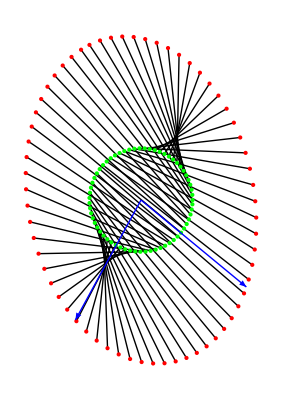

```mathematica
mat5={{-1,2},{3,1}}//N; (*the "//N" will produce normalized eigenvectors*)
{l1,l2}=Eigenvalues[mat5];
{v1,v2}=Eigenvectors[mat5];
Print["Eigenvalues: ",l1,", ",l2];
Print["Eigenvectors (Blue): ",MatrixForm[v1],", ", MatrixForm[v2]];

arrowv1=Graphics[{Thick,Blue,Arrowheads[Large],Arrow[{{0,0},l1*v1}]}];
arrowv2 =Graphics[{Thick,Blue,Arrowheads[Large],Arrow[{{0,0},l2*v2}]}];

circpoints1 = Table[{Cos[t],Sin[t]},{t,0, 2Pi,0.1}];
ellpoints1= Table[mat5.{Cos[t],Sin[t]},{t,0,2Pi,0.1}];
pplot=Graphics[{PointSize[Large],Green,Point[circpoints1],Red, Point[ellpoints1]}];

line[t_]:=Graphics[Line[ {mat5.{Cos[t],Sin[t]},{Cos[t],Sin[t]}}]];
lineplot=Table[line[t],{t,0,2Pi,0.1}];

Show[{lineplot,pplot,arrowv1,arrowv2}]
```

## 3D

Another example of a linear space is given by all 3D vectors v= (x_1
x_2
x_3) . Linear combinations are defined by 
	s_1 v_1 +s_2 v_2 +s_3 v_3;   s_i ϵ ℝ.
	
The zero vector now is 0=(0
0
0).

A matrix is defined by (a_11 | a_12 | a_13
a_21 | a_22 | a_23
a_31 | a_32 | a_33).

Concepts such as matrix multiplication, eigenvalues etc. carry over to the 3D case in complete analogy.
	
The gray triangle in the following cell defines the plane formed by a,b,c (in black, and just for reference). The result of the linear coombinations is shown as a 3D tube vector.

```mathematica
aa = {1,0,0}; (*  Green Arrow *)
bb= {0,1,0}; (*  Red Arrow *)
cc= {0,0,1}; (*  Blue Arrow *)

arrowaa={Arrowheads[Large],Arrow[{{0,0,0},aa}]};
arrowbb ={Arrowheads[Large],Arrow[{{0,0,0},bb}]};
arrowcc ={Arrowheads[Large],Arrow[{{0,0,0},cc}]};
arrowabc ={Arrowheads[.06],Arrow[Tube[{{0,0,0},r*aa+s*bb+t*cc},.005]]};
(*triangle=Polygon[{aa,bb,cc}];*)

Manipulate[
Graphics3D[{ {Arrowheads[.06],Arrow[Tube[{{0,0,0},r*aa+s*bb+t*cc},.005]]},Thick,arrowaa, arrowbb, arrowcc, LightGray,Opacity[0.8],Polygon[{aa,bb,cc}]},Boxed->False,PlotRange->{{-aa[[1]],aa[[1]]},{-bb[[1]],bb[[1]]},{-cc[[1]],cc[[1]]}}],{{r,0.333},-2,2},{{s,0.333},-2,2},{{t,.333},-2,2}]
```

In 3D, matrices map spheres to ellipsoids. An example is inthe next cell.

```mathematica
mmat={{3,2,1},{2,2,2},{1,2,-3}};
sphere[u_,v_]:={Cos[u]*Sin[v],Sin[u]*Sin[v],Cos[v]};
ell[u_,v_]:=mmat.sphere[u,v];

sphereplot=ParametricPlot3D[sphere[u,v],{u,0,2Pi},{v,0,Pi},PlotStyle->{Green,Opacity[0.8]},Mesh-> None,Axes->False,Boxed->False];
ellplot=ParametricPlot3D[ell[u,v],{u,0,2Pi},{v,0,Pi},PlotStyle->{Red,Opacity[0.8]},Mesh-> None,Axes-> False,Boxed->False];

Show[ellplot,sphereplot]
```

-Graphics3D-

## Dimension

A linear space, being a set, has many subsets. Some of these are themselves linear spaces. Example: in 3D, fix any two vectors v and w. Let S[v,w] be the set of all 3D vectors u which may be expressed as linear combinations of v and w: 

	u = rv + sw.
	
Then S[v,w] is a linear space. Since it is determined (spanned) by two vectors, it is called a two-dimensional (2D) subspace of S. Similarly, a 1D subspace is obtained by all multiples of one vector a.

The following cell illustrates the subspace spanned by two vectors v and w (in blue). Note that the variable vector u (pictured tube style) never leaves the colored plane (rotate the image!).

```mathematica
aa1 = {1,0,0};  (*  black *)
bb1= {0,1,0};  (*  black *)
cc1= {0,0,1};  (*  black*)

vv1={1,1,0}; (* blue *)
ww1={0,0,2}; (* blue *)

arrowaa1={Arrowheads[Large],Arrow[{{0,0,0},aa1}]};
arrowbb1 ={Arrowheads[Large],Arrow[{{0,0,0},bb1}]};
arrowcc1 ={Arrowheads[Large],Arrow[{{0,0,0},cc1}]};
arrowvv1 ={Arrowheads[Large],Arrow[{{0,0,0},vv1}]};
arrowww1 ={Arrowheads[Large],Arrow[{{0,0,0},ww1}]};


Manipulate[
Graphics3D[{ {Arrowheads[.06],Arrow[Tube[{{0,0,0},r*vv1+s*ww1},.005]]},Thick,arrowaa1, arrowbb1, arrowcc1,Blue, arrowvv1, arrowww1, LightBlue,Opacity[0.8],Polygon[{-vv1-ww1,-ww1-ww1,vv1+ww1,ww1-vv1+ww1,-vv1}]},Boxed->False,PlotRange->{{-aa1[[1]],aa1[[1]]},{-bb1[[1]],bb1[[1]]},{-cc1[[1]],cc1[[1]]}}],{{r,0.333},-1,1},{{s,0.333},-1,1}]
```

## Rank

A matrix M maps all vectors of a linear space S of dimension d to another linear space S' (because M is a linear map). But S' is not always equal to S -- it may have a lower dimension d'⩽d. Then S' is spanned by a set of d' vectors and is a subspace of S. The dimension d' is called the rank of M. 

In the following cell, 3D space, spanned by three vectors a,b,c (in green), is mapped by a rank 2 matrix. The resulting space is 2D and is shown as a plane with the three image vectors (in red) -- make sure to rotate the image! By manipulating r and s in Manipulate, the matrix changes, and so does the plane.

```mathematica
aa2 = {1,0,0};  (*  green *)
bb2= {0,1,0};  (*  green *)
cc2= {0,0,1};  (*  green*)
range2=Max[Norm[aa2],Norm[bb2],Norm[cc2]];
mm1={-1,1,-1};
mm2={1,.5,.5};

arrowaa2={Green,Arrowheads[Large],Arrow[{{0,0,0},aa2}]};
arrowbb2 ={Green,Arrowheads[Large],Arrow[{{0,0,0},bb2}]};
arrowcc2 ={Green,Arrowheads[Large],Arrow[{{0,0,0},cc2}]};


Manipulate[mmat2={mm1,mm2,r*mm1+s*mm2};(* mmat has rank 2 *)
vrsa=mmat2.aa2;
vrsb=mmat2.bb2;
vrsc=mmat2.cc2;
arrowrsaa2={Arrowheads[Large],Arrow[{{0,0,0},vrsa}]};
arrowrsbb2 ={Arrowheads[Large],Arrow[{{0,0,0},vrsb}]};
arrowrscc2 ={Arrowheads[Large],Arrow[{{0,0,0},vrsc}]};

pica=Graphics3D[{ {Arrowheads[.06]},Thick,arrowaa2, arrowbb2, arrowcc2,Red, arrowrsaa2,arrowrsbb2,arrowrscc2,LightRed,Opacity[0.8],Polygon[{{0,0,0},vrsa,vrsb,{0,0,0}}]},Boxed->False,PlotRange->range2];picb=Graphics3D[{ {Arrowheads[.06]},Thick,arrowaa2, arrowbb2, arrowcc2,Red, arrowrsaa2,arrowrsbb2,arrowrscc2,LightRed,Opacity[0.8],Polygon[{{0,0,0},vrsa,vrsc,{0,0,0}}]},Boxed->False,PlotRange->range2];picc=Graphics3D[{ {Arrowheads[.06]},Thick,arrowaa2, arrowbb2, arrowcc2,Red, arrowrsaa2,arrowrsbb2,arrowrscc2,LightRed,Opacity[0.8],Polygon[{{0,0,0},vrsb,vrsc,{0,0,0}}]},Boxed->False,PlotRange->range2];Show[{pica,picb,picc}],{{r,0.333},-1,1},{{s,0.333},-1,1}]
```

Which vectors of S are mapped to the zero vector by M? Those are vectors of a (d-d')-dimensional space N, called the null space of M. In the case of the above notebook, d-d'=1; thus N is spanned by just one vector. It is shown as a tube vector in the following cell.

```mathematica
aa3 = {1,0,0};  (*  green *)
bb3= {0,1,0};  (*  green *)
cc3= {0,0,1};  (*  green*)
range3=Max[Norm[aa3],Norm[bb3],Norm[cc3]];
mm13={-1,1,-1};
mm23={1,.5,.5};

arrowaa3={Green,Arrowheads[Large],Arrow[{{0,0,0},aa3}]};
arrowbb3 ={Green,Arrowheads[Large],Arrow[{{0,0,0},bb3}]};
arrowcc3 ={Green,Arrowheads[Large],Arrow[{{0,0,0},cc3}]};


Manipulate[mmat3={mm13,mm23,r*mm13+s*mm23};(* mmat3 has rank 2 *)
nn=NullSpace[mmat3];
vrsa1=mmat3.aa3;
vrsb1=mmat3.bb3;
vrsc1=mmat3.cc3;
arrowrsa={Arrowheads[Large],Arrow[{{0,0,0},vrsa1}]};
arrowrsb ={Arrowheads[Large],Arrow[{{0,0,0},vrsb1}]};
arrowrsc ={Arrowheads[Large],Arrow[{{0,0,0},vrsc1}]};
arrownn={Arrowheads[.06],Arrow[Tube[{{0,0,0},nn[[1]]},.005]]};

pica1=Graphics3D[{ {Arrowheads[.06]},Thick,arrowaa3, arrowbb3, arrowcc3,arrownn,Red, arrowrsa,arrowrsb,arrowrsc,LightRed,Opacity[0.8],Polygon[{{0,0,0},vrsa1,vrsb1,{0,0,0}}]},Boxed->False,PlotRange->range3];picb1=Graphics3D[{ {Arrowheads[.06]},Thick,arrowaa3, arrowbb3, arrowcc3,Red, arrowrsa,arrowrsb,arrowrsc,LightRed,Opacity[0.8],Polygon[{{0,0,0},vrsa1,vrsc1,{0,0,0}}]},Boxed->False,PlotRange->range3];picc1=Graphics3D[{ {Arrowheads[.06]},Thick,arrowaa3, arrowbb3, arrowcc3,Red, arrowrsa,arrowrsb,arrowrsc,LightRed,Opacity[0.8],Polygon[{{0,0,0},vrsb1,vrsc1,{0,0,0}}]},Boxed->False,PlotRange->range3];Show[{pica1,picb1,picc1}],{{r,0.333},-1,1},{{s,0.333},-1,1}]
```

## Determinants

Three vectors a,b,c span a parallelepiped ( a skew box). It volume is given by the determinant of a,b,c. If it is nonzero, the vectors are linearly independent.

```mathematica
aa4 = {1,0,0};  (*  green *)
bb4= {0,1,0};  (*  green *)
cc4= {0,0,1};  (*  green*)
range4=1.5Max[Norm[aa4],Norm[bb4],Norm[cc4]];

arrowaa4={Green,Arrowheads[Large],Arrow[{{0,0,0},aa4}]};
arrowbb4 ={Green,Arrowheads[Large],Arrow[{{0,0,0},bb4}]};
arrowcc4 ={Green,Arrowheads[Large],Arrow[{{0,0,0},cc4}]};
zz={0,0,0};

Manipulate[
rst={r,s,t};
(*arrowrst ={Arrowheads[Large],Arrow[{{0,0,0},rst}]};*)
pic4=Graphics3D[{ Arrowheads[.05],Arrow[Tube[{{0,0,0},rst},.015]],Thick,arrowaa4, arrowbb4, arrowcc4,LightRed,Opacity[0.8],
Polygon[{zz,aa4,aa4+bb4,bb4}],
Polygon[{zz,aa4,aa4+rst,rst}],
Polygon[{zz,bb4,bb4+rst,rst}],
Polygon[{rst+zz,rst+aa4,rst+aa4+bb4,rst+bb4}],
Polygon[{bb4+zz,bb4+aa4,bb4+aa4+rst,bb4+rst}],
Polygon[{aa4+zz,aa4+bb4,aa4+bb4+rst,aa4+rst}]
},Boxed->False,PlotRange->range4,PlotLabel->Style[Framed[Det[{aa4,bb4,rst}]],20]];
Show[pic4],{{r,0},-1,1},{{s,0},-1,1},{{t,1},-1,1}]
```